## CHSH game

More details on Bell’s theorem: read our documentation

CHSH stands for John Clauser, Michael Horne, Abner Shimony, and Richard Holt

```mathematica
chsh=QuantumCircuitOperator["CHSH"]
```

QuantumCircuitOperator[…]

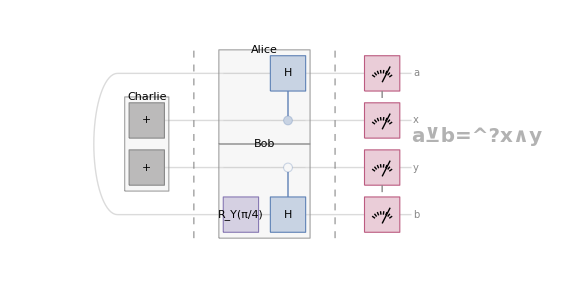

```mathematica
chsh["Diagram",]
```

Charlie is a referee sending random 0 or 1 to Alice and Bob
Let’s look at the statistics of Charlie

```mathematica
plus=QuantumMeasurementOperator[]@QuantumState["+"]
```

QuantumMeasurement[…]

Plot probabilities (quantum predictions)

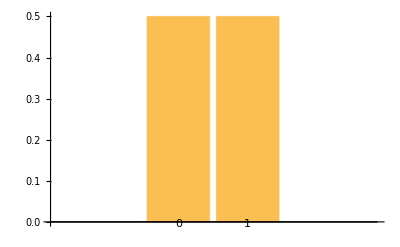

```mathematica
plus["ProbabilityPlot"]
```

Simulate the measurement and count results

```mathematica
plus["SimulatedMeasurement",10^3]//Counts
```

<|0→526,1→474|>

### Classical approach to win CHSH game

Create 10^4 random {0,1} pairs

```mathematica
xy=RandomChoice[{0,1},{10^4,2}];
```

Alice and Bob strategy: report only 0, no matter what Charlie sends

```mathematica
ab=ConstantArray[0,{10^4,2}];
```

Merge data from Charlie and what Alice and Bob report

```mathematica
sequence=Transpose[{xy,ab}];
```

Show some of them

```mathematica
TableForm[sequence[[;;10]],TableDepth->2,TableHeadings->{None, {"{x,y}","{a,b}"}}]
```

{x,y} | {a,b}
{0,1} | {0,0}
{0,1} | {0,0}
{0,0} | {0,0}
{1,1} | {0,0}
{1,1} | {0,0}
{0,0} | {0,0}
{1,1} | {0,0}
{1,0} | {0,0}
{1,1} | {0,0}
{1,1} | {0,0}

Count only the winning results (classical approach: never more than 75%)

```mathematica
Length[Cases[sequence,{{x_,y_},{a_,b_}}/;BitAnd[x,y]==BitXor[a,b]]]/10^4//N
```

0.7475

### Quantum approach to win CHSH game

Alice and Bob can use a Bell state (manipulate quantum entanglement)

```mathematica
chsh["Diagram",]
```

-Graphics-

Calculate probabilities

```mathematica
Probability[BitAnd[x,y]==BitXor[a,b],{a,x,y,b}\[Distributed]QuantumCircuitOperator["CHSH"][]["MultivariateDistribution"]]
```

(2+√2)/(4 (1/8 (2-√2)+1/4 (2+√2)+1/2 Sin[π/8]^2))

```mathematica
NProbability[BitAnd[x,y]==BitXor[a,b],{a,x,y,b}\[Distributed]QuantumCircuitOperator["CHSH"][]["MultivariateDistribution"]]
```

0.853553

## Simon algorithm

Simon’s algorithm is a quantum algorithm designed to solve the Simon’s problem efficiently. It aims to find a hidden bitstring ‘s’ by querying a black-box function. The key insight involves exploiting quantum parallelism to derive information about ‘s’ through a series of quantum operations, demonstrating exponential speedup compared to classical algorithms.

A secret sequence

```mathematica
seq={1,0,1,1};
```

Create corresponding Simon oracle

```mathematica
simonOracle=QuantumCircuitOperator["SimonOracle"[StringJoin@IntegerString@seq]]
```

QuantumCircuitOperator[…]

Diagram

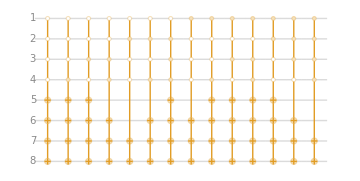

```mathematica
simonOracle["Diagram"]
```

Show the effect of oracle

```mathematica
boolTable[oracle_]:=KeyValueMap[Function[u,PadRight[u,n]]/@Cases[{#1["Formula"],#2["Formula"]},QuditName[x_List,___]:>x,All]&]@AssociationMap[QuantumOperator["Discard"->Range[n]][oracle[#]]&,QuantumBasis[2,n]["BasisStates"]]
TableForm[boolTable[simonOracle],TableDepth->2,TableHeadings->{None,{"bit","oracl[bit]"}}]
```

bit | oracl[bit]
{0,0,0,0} | {1,1,1,1}
{0,0,0,1} | {1,1,1,1}
{0,0,1,0} | {1,1,1,1}
{0,0,1,1} | {0,1,1,1}
{0,1,0,0} | {0,0,1,1}
{0,1,0,1} | {0,1,1,1}
{0,1,1,0} | {0,0,0,0}
{0,1,1,1} | {1,1,1,1}
{1,0,0,0} | {0,1,1,1}
{1,0,0,1} | {1,1,1,1}
{1,0,1,0} | {1,1,1,1}
{1,0,1,1} | {1,1,1,1}
{1,1,0,0} | {1,1,1,1}
{1,1,0,1} | {0,0,0,0}
{1,1,1,0} | {0,1,1,1}
{1,1,1,1} | {0,0,1,1}

Create the full circuit

```mathematica
n=Length[seq];
simon=QuantumCircuitOperator[{"H"->Range[n],simonOracle,"H"->Range[n],Range[n]}]
```

QuantumCircuitOperator[…]

Diagram

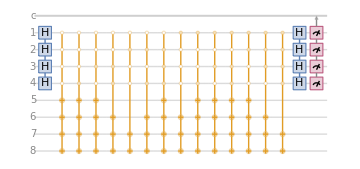

```mathematica
simon["Flatten"]["Diagram"]
```

Evaluate the Simon circuit

```mathematica
simonMeas=N[simon][]
```

QuantumMeasurement[…]

Plot probabilities

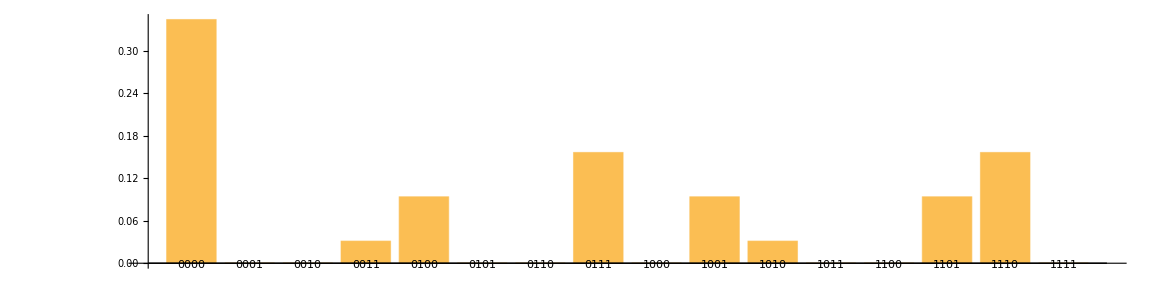

```mathematica
simonMeas["ProbabilityPlot",AspectRatio->1/4]
```

List of all potential results

```mathematica
m=Normal/@Keys@Select[simonMeas["Probabilities"],Positive]
```

{{0,0,0,0},{0,0,1,1},{0,1,0,0},{0,1,1,1},{1,0,0,1},{1,0,1,0},{1,1,0,1},{1,1,1,0}}

Find the null vector (matric.m=0) modul 2

```mathematica
NullSpace[m,Modulus->2]
```

{{1,0,1,1}}

We found the secret bit

```mathematica
seq==%[[1]]
```

True